```mathematica
p[n_,x_]:=Simplify[HermiteH[n,x/Sqrt[.2]]/2^(n/2)]
"Renormalized Hermit Polinomials";
pn[n_,x_]:=Simplify[HermiteH[n,x/Sqrt[.2]]/(2^(n/2)Sqrt[n! Sqrt[2 Pi]])]
"Normalized Hermit Polinomials";
u[n_,x_]:=p[n,x]Exp[-.2x^2]
"Transformation functions";
sc[n_,m_]:=SeriesCoefficient[p[n,x],{x,0,m}]
"Coefficients of Renormalized Hermit Polinomials to Define Diff Operators";
Vu[sigma__Integer,x_]:=Simplify[.2x^2-2D[Log[If
[Length[{sigma}]>1,Wronskian[p[{sigma},x/Sqrt[.2]],x],Wronskian[{p[{sigma},x/Sqrt[.2]]},x]]],x,x]+Length[{sigma}]];
"Special form of Darboux-transformed potential with transformation functions being eigen-functions. This potentials correspond to the isochronous Green functions";
dVu[sigma__Integer,x_]:=Simplify[-2D[Log[If
[Length[{sigma}]>1,Wronskian[p[{sigma},x/Sqrt[.2]],x],Wronskian[{p[{sigma},x]},x]]],x,x]+Length[{sigma}]];
```

```mathematica
TransPolUh[sigma__Integer,x_,n_]:=If[Product[{sigma}[[i]]-n,{i,1,Length[{sigma}]}]==0,0,Product[{sigma}[[i]]-n,{i,1,Length[{sigma}]}]^(-1/2) Wronskian[Join[pn[{sigma},x/Sqrt[.2]],{pn[n,x/Sqrt[.2]]}],x]];
```

```mathematica
Wt[sigma__Integer,x_]:=Wronskian[pn[{sigma},x/Sqrt[.2]],x]
Psi0[sigma__Integer,x_]:=TransPolUh[sigma,x/Sqrt[.2],0]Exp[-.2x^2]/Wt[sigma,x/Sqrt[.2]]
```

```mathematica
"For a given sequence sigma we define connection polynomials Q";
n0=1/(pn[0,x/Sqrt[.2]]pn[0,y/Sqrt[.2]]);
sigma={3,4}/.List->Sequence
"Polynomials read"
Qpol[0]=n0 TransPolUh[sigma,x/Sqrt[.2],0]TransPolUh[sigma,y/Sqrt[.2],0]
For[i=1,i<{sigma}[[-1]]+2,i++,Qpol[i]=FullSimplify[n0(TransPolUh[sigma,x/Sqrt[.2],i]TransPolUh[sigma,y/Sqrt[.2],i]-Sum[pn[j,y/Sqrt[.2]]pn[j,x/Sqrt[.2]]Qpol[i-j],{j,1,i}])];Print[Qpol[i]]]
"Sum of polynomials reads"
Simplify[Sum[Qpol[i],{i,0,{sigma}[[-1]]+1}]]
```

Sequence[3,4]

Polynomials read

((3+x^4) (3+y^4))/(24 π)

-(x y (9-6 y^2+3 y^4+x^4 (3-2 y^2+y^4)-2 x^2 (3+2 y^2+y^4)))/(48 π)

(9 (1+y^2) (3-6 y^2+y^4)+x^6 (9+9 y^2-3 y^4+y^6)+9 x^2 (-3+9 y^2+y^4+y^6)-3 x^4 (15-3 y^2+7 y^4+y^6))/(288 π)

(x y (x^4 (3-2 y^2+y^4)+3 (-9+2 y^2+y^4)-2 x^2 (-3+4 y^2+y^4)))/(48 π)

-(3-6 y^2+y^4+x^4 (1+2 y^2-y^4)+2 x^2 (-3+y^4))/(16 π)

(x (-3+x^2) y (-3+y^2))/(12 π)

Sum of polynomials reads

((9+9 x^2-3 x^4+x^6) (9+9 y^2-3 y^4+y^6))/(288 π)

Sequence[3,4]

Potential sigma

(-648+5265 x^2-2214 x^4-549 x^6+36 x^8+27 x^10+2 x^12+x^14)/(4 (9+9 x^2-3 x^4+x^6)^2)

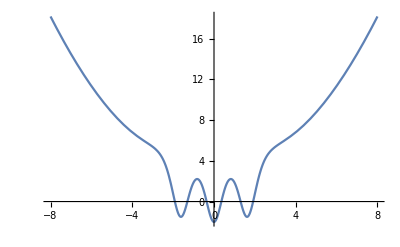

```mathematica
Kosc[x_,y_,t_]:=Exp[I((x^2/Sqrt[.2]+y^2/Sqrt[.2])Cos[t]-2 (x y)/Sqrt[.2])/(4Sin[t])]/Sqrt[4 Pi I Sin[t]]
Wt[x_]:=Wronskian[pn[{sigma},x/Sqrt[.2]],x]
"Propagator of oscillator";
Ks[x_,y_,t_]:=Kosc[x,y,t]Sum[Qpol[k]Exp[-I t k],{k,0,{sigma}[[-1]]+1}]/(Wt[x] Wt[y])
"Propagator for the rationally extended oscillator with given sigma";
sigma
"Potential sigma"
Vsigma=Vu[sigma,x]
Plot[{Vsigma},{x,-8,8}]
```